```mathematica
Import["../libs/QuantumDavid.m"]
```

```mathematica
x=Import["trazas.txt","Table"]//ToExpression;
```

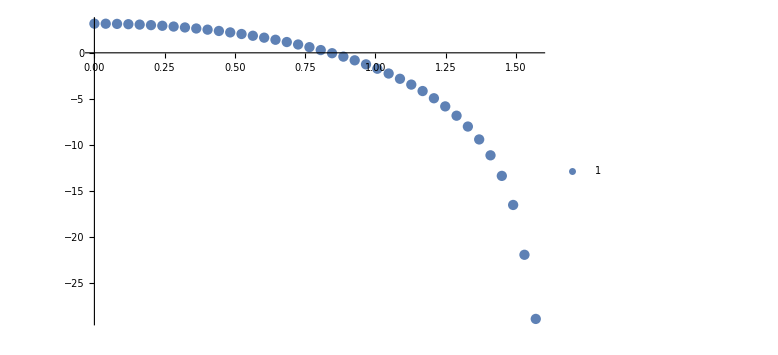
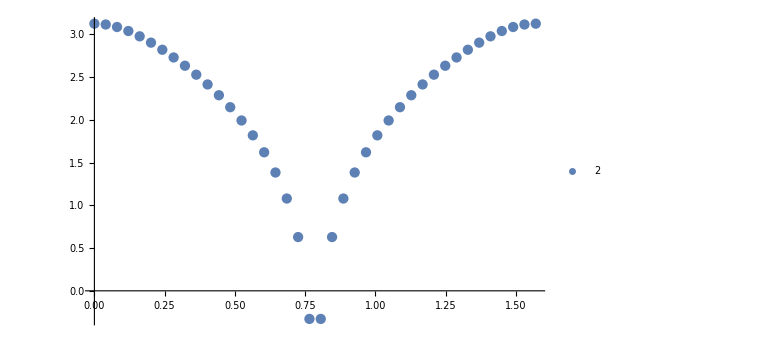
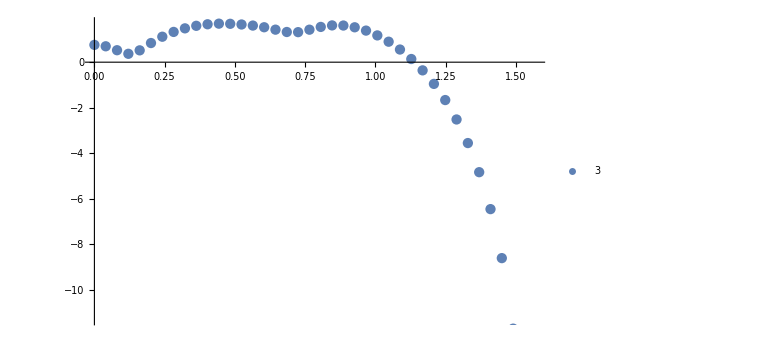
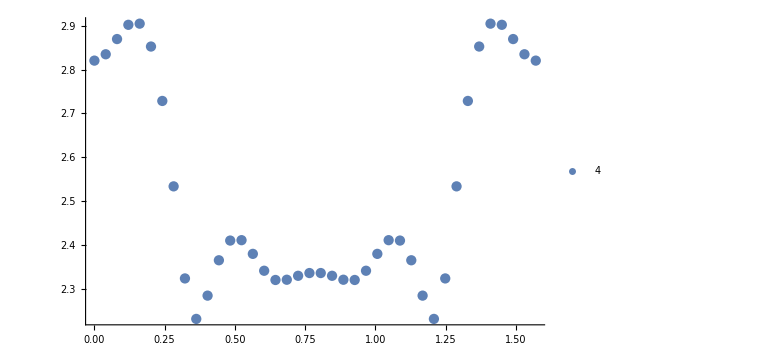
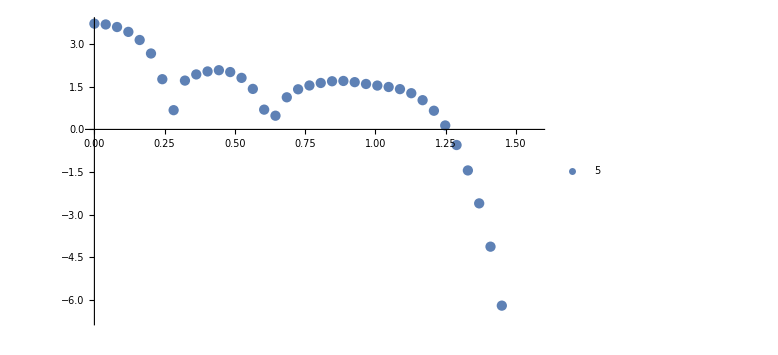
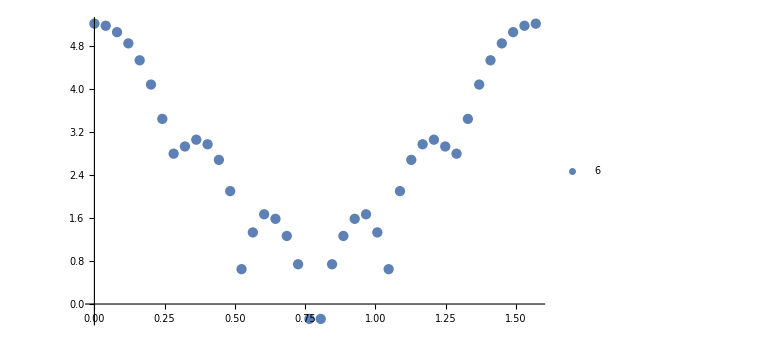
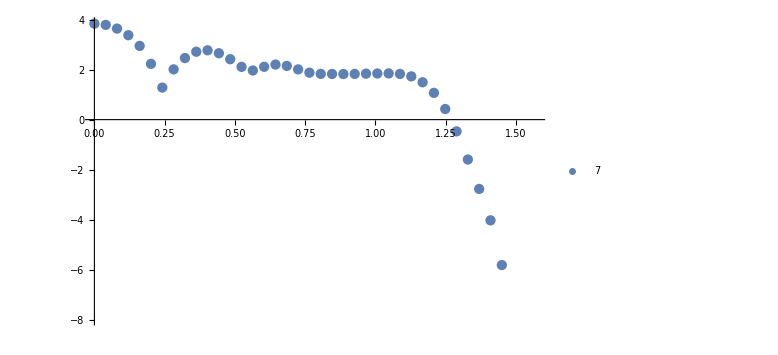
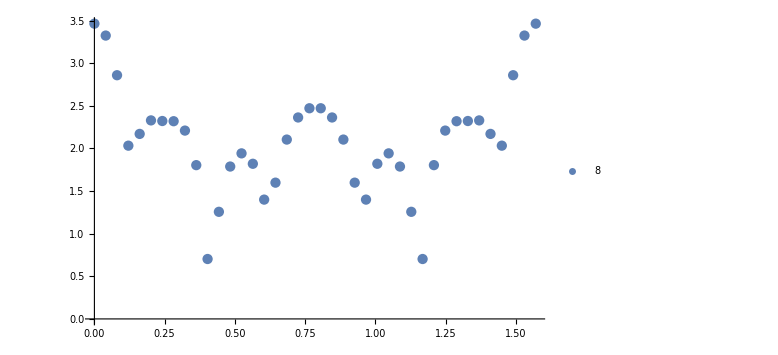

```mathematica
Table[ListPlot[Table[{linearmesh[0,Pi/2,40][[i]],Log[10,Abs[x[[k]][[i]]]^2]},{i,1,40}],ImageSize->Large,PlotLegends->{ToString[k]}],{k,1,12}]
```